```mathematica
PredicateName[p_Symbol]:= p (* Special case usable for simpler representation of propositional logic *)
PredicateName[p_[x___]]:=p
PredicateSymbols[Not[a_]] := PredicateSymbols[a]
PredicateSymbols[a_∧b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[a_∨b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[a_⇒b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[p_Symbol[x_]]:= {{p, 1}}
PredicateSymbols[p_Symbol[x_,y_]]:={{p,2}}
FOAtoms[False] := {}
FOAtoms[True] := {}
FOAtoms[Not[ϕ_]] := FOAtoms[ϕ]
FOAtoms[ϕ_∧ψ_]:= FOAtoms[ϕ]∪FOAtoms[ψ]
FOAtoms[ϕ_∨ψ_]:= FOAtoms[ϕ]∪FOAtoms[ψ]
FOAtoms[ϕ_⇒ψ_]:= FOAtoms[ϕ]∪FOAtoms[ψ]
FOAtoms[atom_]:= {atom}
PositiveAtoms[model_List]:=model/.{(a_->False) :> Nothing, (a_->True) :> a}
NegativeAtoms[model_List]:=model/.{(a_->True) :> Nothing, (a_->False) :> a}
PredicateSymbol[p_Symbol[x___]]:= {p, Length[x]}
PredicateSymbols[ϕ_]:= PredicateSymbol/@ FOAtoms[ϕ]
MakeLiteral[a_->True]:= a
MakeLiteral[b_->False]:= ¬b
InterpretationToFormula[f_List]:= And@@(MakeLiteral /@ f)
SymbolSetWeight[set_List, weights_]:= Times@@ (weights /@set)
GroundAtomSetWeight[set_List, weights_]:=SymbolSetWeight[PredicateName/@ set, weights]
ModelWeight[model_, weightsPositive_, weightsNegative_]:= (* FIXME - this should be easy to make 2x faster *)
GroundAtomSetWeight[PositiveAtoms[model], weightsPositive] * GroundAtomSetWeight[NegativeAtoms[model], weightsNegative]
AllModels[False]:= {};
AllModels[True]:={{}};
AllModels[ϕ_]:= Module[
{variables= {f[a,a],f[a,b], f[b,a],f[b,b]}}, (* FIXME - this is probably wrong in general, if not justify why *)
(modelBool↦Thread[variables->modelBool])/@
SatisfiabilityInstances[ϕ,variables,All]
]
WeightedModels[ϕ_,weightsPositive_, weightsNegative_]:=Total[ (*naive WMC implementation using SAT *)
(model ↦ModelWeight[model, weightsPositive, weightsNegative])/@
AllModels[ϕ]
]
PredicateToAtom[{p_,1}]:= p[a]
PredicateToAtom[{p_,2}]:= p[a,a]
CellAtoms[predicates_List]:=PredicateToAtom/@ predicates
(*MakeCell[atoms_List,fs_List]:=  And@@MapThread[#1[#2]&,{fs,atoms}] *)(* just a helper function for AllCells *)
MakeCell[atoms_List,boolVec_List]:= Thread[atoms->boolVec]
AllCells[atoms_List]:=
(boolVec ↦MakeCell[atoms,boolVec])/@
Tuples[{False,True}, Length[atoms]]
FormulaCells[ϕ_]:= AllCells@CellAtoms@PredicateSymbols[ϕ]
SwapVariables[object_]:= object /. {a->b, b->a}
FormulaSymmetric[ψ_]:=ψ∧SwapVariables[ψ]
FormulaReflexive[ψ_]:= ψ /. b->a
FormulaSimplified1Cell[ψ_,cell_] := ψ /.Join[cell, SwapVariables[cell]]
FormulaSimplified2Cell[ψ_,cell1_, cell2_] := FormulaSymmetric[ψ] /.Join[cell1, SwapVariables[cell2]]
FormulaSimplified[ψ_, cell1_, cell2_]:=FormulaSymmetric[ψ] /.Join[cell1, SwapVariables[cell2]]
FormulaSimplified[ψ_,cell_]:=FormulaSimplified[ψ, cell, cell]
RTerm[ψ_,cell1_,cell2_,weightsPositive_, weightsNegative_]:=
WeightedModels[
FormulaSimplified2Cell[ψ, cell1, cell2],
weightsPositive, weightsNegative
]
STerm[ψ_,cell_,weightsPositive_, weightsNegative_]:=
WeightedModels[
FormulaSimplified1Cell[ψ, cell]∧SwapVariables@FormulaSimplified1Cell[ψ, cell],
weightsPositive, weightsNegative
]
WTerm[ψ_,cell_,weightsPositive_, weightsNegative_]:=
WeightedModels[
FormulaSimplified1Cell[FormulaReflexive[ψ], cell],
weightsPositive, weightsNegative
]
(*
STerm[ψ_,cell_,weightsPositive_, weightsNegative_]:=RTerm[FormulaSymmetric[ψ], cell, cell, weightsPositive,weightsNegative];
WTerm[ψ_,cell_,weightsPositive_, weightsNegative_]:=RTerm[FormulaReflexive[ψ], cell, cell, weightsPositive,weightsNegative]
*)
STerms[ψ_, weightsPositive_, weightsNegative_]:= (cell↦STerm[ψ, cell, weightsPositive,weightsNegative]) /@ FormulaCells[ψ]
WTerms[ψ_, weightsPositive_, weightsNegative_]:= (cell↦WTerm[ψ, cell, weightsPositive,weightsNegative]) /@ FormulaCells[ψ]
RTerms[ψ_, weightsPositive_, weightsNegative_] := Module[
{cells = FormulaCells[ψ], length},
length = Length[cells];
(row ↦PadRight[row, length]) /@
Table[
RTerm[ψ, cells⟦i⟧, cells⟦j⟧, weightsPositive,weightsNegative],
{i, 1, length},{j, i+1, length}
]
]
Compatible[i_Integer, cliquePart_List, {s_,w_,r_}]:=Module[{
all=Range@Length[s],
cond3= {j_,k_}:> j<k⇒ r⟦i,k⟧==r⟦j,k⟧,
cond4= {j_,k_,l_}:> (i<j∧k<l)⇒ r⟦i,j⟧==r⟦k,l⟧
},
And[
AllTrue[cliquePart,j↦s⟦i⟧==s⟦j⟧],
AllTrue[cliquePart,j↦w⟦i⟧==s⟦j⟧],
And@@Tuples[{cliquePart,Complement[all, cliquePart]}]/.cond3,
And@@Tuples[{cliquePart, cliquePart, cliquePart}]/.cond4
]
]
Cliques[{s_,w_,r_}]:=Module[
{i, j, cliques={}, length = Length[s],current, all},
all = Range[length];
While[Length[all]>0,
current = {};
(cell↦ If[
Compatible[cell, current, {s,w,r}] ,
AppendTo[current, cell]; all = all /. cell -> Nothing;
]
) /@ all;
AppendTo[cliques, current]
];
cliques
]
(*
GetGTerm[0, n_Integer,cliqueIds_List]:= GetGTerm[0, n,cliqueIds] = Module[
(i↦ ) /@ Range[1,k]
]
GetGTerm[p_Integer, n_Integer,cliqueIds_List]:= GetGTerm[p, n,cliqueIds] = Module[
{s=0},
]*)
GetDTerm[c_, k_,n_] := GetDTerm[c,1, k,n] 
GetDTerm[c_,i_, k_,n_] := Nothing
```

```mathematica
exampleDerangements= ¬f[a,a] ∧ (f[a,b]⇒s1[a])∧(f[b,a]⇒s2[a])
weightsPositiveDerangements=<|f->f,s1->1,s2->1|>
weightsNegativeDerangements=<|f->1,s1->-1,s2->-1|>
s=STerms[exampleDerangements, weightsPositiveDerangements, weightsNegativeDerangements]
w=WTerms[exampleDerangements, weightsPositiveDerangements, weightsNegativeDerangements]
r=RTerms[exampleDerangements, weightsPositiveDerangements, weightsNegativeDerangements];
MatrixForm[r]
Cliques[{s,w,r}]
```

!f[a,a]&&(f[a,b]⇒s1[a])&&(f[b,a]⇒s2[a])

<|f→f,s1→1,s2→1|>

<|f→1,s1→-1,s2→-1|>

{1,1,1,1,0,0,0,0}

{1,1,1,1,0,0,0,0}

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{{1},{2,3,4},{5,6,7,8}}

```mathematica
Compatible[7,{8}, {s,w,r}]
```

True

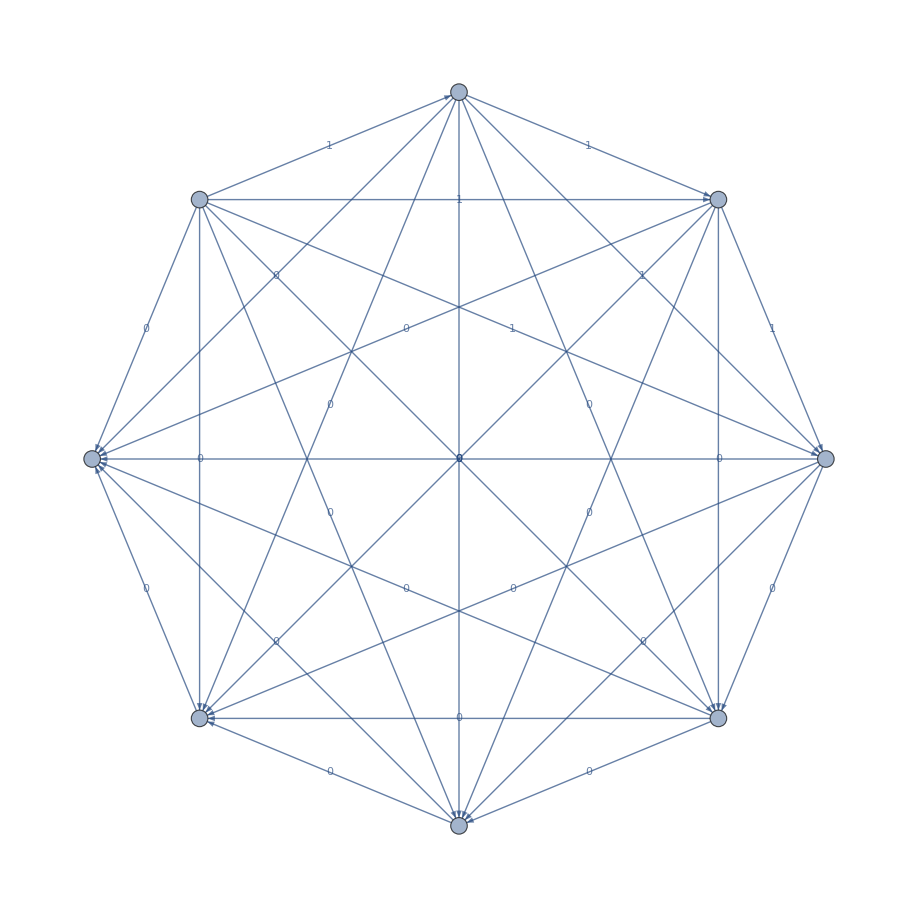

```mathematica
CellGraphEdges[cells_] := Flatten[Table[cells⟦i⟧-> cells⟦j⟧, {j, 1, Length[cells]},{i,1,j-1}],2]
CellGraph[ϕ_,weightsPositive_, weightsNegative_]:= Module[
{
cells =FormulaCells[ϕ],
edgeLabeling = (cell1_->cell2_):> (
(cell1->cell2) ->
RTerm[ϕ, cell1,cell2, weightsPositive, weightsNegative]),
vertexLabeling=cell↦(
cell ->{
STerm[ϕ, cell, weightsPositive, weightsNegative],
WTerm[ϕ, cell, weightsPositive, weightsNegative]})
},
With[
{edges= CellGraphEdges[cells]},
Graph[
edges,
EdgeLabels-> edges /. edgeLabeling,
VertexLabels->(vertexLabeling) /@ cells,
GraphLayout->"CircularEmbedding"
]
]
]
g=CellGraph[exampleDerangements,weightsPositiveDerangements,weightsNegativeDerangements]
```

```mathematica
(* Implementation of WFOMC according to formula (1) in Faster Lifting for Two-Variable Logic using Cell Graphs *)
OrderedPartitions[n_Integer,m_Integer]:= Flatten[
Permutations[PadRight[#,m]]&
/@IntegerPartitions[n,m],
1]
Pow[0,0]:=1
Pow[a_,b_]:=a^b
WFOMC1[ϕ_,n_,weightsPositive_, weightsNegative_]:= Module[{
s=STerms[ϕ, weightsPositive, weightsNegative],
w=WTerms[ϕ, weightsPositive, weightsNegative],
r=RTerms[ϕ, weightsPositive, weightsNegative],
u=2^(Length@PredicateSymbols[ϕ] ),
i,j},
Total[(partition |-> 
Multinomial[Sequence@@partition] *
Product[
r⟦i,j⟧~Pow~(partition⟦i⟧*partition⟦j⟧),
{j,1,u},
{i,1 , j-1}]*
Product[
s⟦i⟧~Pow~Binomial[partition⟦i⟧,2] *
 w⟦i⟧~Pow~partition⟦i⟧,
{i,1,u}]
) /@ OrderedPartitions[n, u]]
]
```

```mathematica
Table[
Expand@WFOMC1[exampleDerangements,n,weightsPositiveDerangements,weightsNegativeDerangements],
 {n, 0, 5}] // Column
```

1
4
8+14 f+7 f^2
16+90 f+225 f^2+300 f^3+225 f^4+90 f^5+15 f^6
32+372 f+2046 f^2+6820 f^3+15345 f^4+24552 f^5+28644 f^6+24552 f^7+15345 f^8+6820 f^9+2046 f^10+372 f^11+31 f^12
64+1260 f+11970 f^2+71820 f^3+305235 f^4+976752 f^5+2441880 f^6+4883760 f^7+7936110 f^8+10581480 f^9+11639628 f^10+10581480 f^11+7936110 f^12+4883760 f^13+2441880 f^14+976752 f^15+305235 f^16+71820 f^17+11970 f^18+1260 f^19+63 f^20

```mathematica
Table[Subfactorial[i],{i,0,5}]
```

{1,0,1,2,9,44}

```mathematica
Table[
Expand@WFOMC1[exampleDerangements,n,weightsPositiveDerangements,weightsNegativeDerangements],
 {n, 0, 5}]//Column
```

{{1}}
{{1,1,1,1,0,0,0,0}}
{{1,1,1,1,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
{{1,1,1,1,0,0,0,0,3,3,0,0,0,0,0,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
{{1,1,1,1,0,0,0,0,4,4,0,0,0,0,0,4,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
{{1,1,1,1,0,0,0,0,5,5,0,0,0,0,0,5,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,10,0,0,0,0,0,10,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
exampleDerangements
FormulaCells[exampleDerangements]
FormulaSimplified[exampleDerangements, {f[a,a]->False,s1[a]->False,s2[a]->False}, {f[a,a]->False,s1[a]->False,s2[a]->True}]
```

!f[a,a]&&(f[a,b]⇒s1[a])&&(f[b,a]⇒s2[a])

{{f[a,a]→False,s1[a]→False,s2[a]→False},{f[a,a]→False,s1[a]→False,s2[a]→True},{f[a,a]→False,s1[a]→True,s2[a]→False},{f[a,a]→False,s1[a]→True,s2[a]→True},{f[a,a]→True,s1[a]→False,s2[a]→False},{f[a,a]→True,s1[a]→False,s2[a]→True},{f[a,a]→True,s1[a]→True,s2[a]→False},{f[a,a]→True,s1[a]→True,s2[a]→True}}

!f[a,b]&&!f[b,a]&&!f[b,a]

```mathematica
FormulaSymmetric[exampleDerangements, {f[a,a]->False,s1[a]->False,s2[a]->True}]
```

FormulaSymmetric[!f[a,a]&&(f[a,b]⇒s1[a])&&(f[b,a]⇒s2[a]),{f[a,a]→False,s1[a]→False,s2[a]→True}]

```mathematica
ModelWeight[#, weightsPositiveDerangements,weightsNegativeDerangements]&/@AllModels[exampleDerangements]
```

{f^2,f,f,1,-f,-f,-1,-1,1}

```mathematica
WeightedModels[exampleDerangements, weightsPositiveDerangements,weightsNegativeDerangements]
```

f^2

```mathematica
r
```

{{1,1,1,0,0,0,0,0},{1,1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
models =AllModels[!f[b,a]&&!f[a,a], f[b,a]&&f[a,a]&&f[a,b]&&s1[a]&&s1[b]];
Column[models]
ModelWeight[#,weightsPositiveDerangements,weightsNegativeDerangements]&/@models 
Total[%]
```

Column[AllModels[!f[b,a]&&!f[a,a],f[b,a]&&f[a,a]&&f[a,b]&&s1[a]&&s1[b]]]

AllModels[GroundAtomSetWeight[NegativeAtoms[!f[b,a]&&!f[a,a]],<|f→1,s1→-1,s2→-1|>] GroundAtomSetWeight[PositiveAtoms[!f[b,a]&&!f[a,a]],<|f→f,s1→1,s2→1|>],GroundAtomSetWeight[NegativeAtoms[f[b,a]&&f[a,a]&&f[a,b]&&s1[a]&&s1[b]],<|f→1,s1→-1,s2→-1|>] GroundAtomSetWeight[PositiveAtoms[f[b,a]&&f[a,a]&&f[a,b]&&s1[a]&&s1[b]],<|f→f,s1→1,s2→1|>]]

Total[AllModels[GroundAtomSetWeight[NegativeAtoms[!f[b,a]&&!f[a,a]],<|f→1,s1→-1,s2→-1|>] GroundAtomSetWeight[PositiveAtoms[!f[b,a]&&!f[a,a]],<|f→f,s1→1,s2→1|>],GroundAtomSetWeight[NegativeAtoms[f[b,a]&&f[a,a]&&f[a,b]&&s1[a]&&s1[b]],<|f→1,s1→-1,s2→-1|>] GroundAtomSetWeight[PositiveAtoms[f[b,a]&&f[a,a]&&f[a,b]&&s1[a]&&s1[b]],<|f→f,s1→1,s2→1|>]]]

```mathematica
WeightedModels[!f[b,a], exampleDerangements,weightsPositiveDerangements,weightsNegativeDerangements]&/@AllModels[!f[b,a],exampleDerangements]
```

AllModels[WeightedModels[!f[b,a],!f[a,a]&&(f[a,b]⇒s1[a])&&(f[b,a]⇒s2[a]),<|f→f,s1→1,s2→1|>,<|f→1,s1→-1,s2→-1|>],WeightedModels[!f[b,a],!f[a,a]&&(f[a,b]⇒s1[a])&&(f[b,a]⇒s2[a]),<|f→f,s1→1,s2→1|>,<|f→1,s1→-1,s2→-1|>]]

```mathematica
SatisfiabilityInstances[Equivalent[a,b],{a,b,c},All]
```

{{True,True,True},{False,False,True},{True,True,False},{False,False,False}}

```mathematica
FOAtoms[exampleDerangements]/. f_[x_]:> Nothing
```

{f[a,a],f[a,b],f[b,a]}

```mathematica
InterpretationToFormula/@FormulaCells[exampleDerangements]
```

{!f[a,a]&&!s1[a]&&!s2[a],!f[a,a]&&!s1[a]&&s2[a],!f[a,a]&&s1[a]&&!s2[a],!f[a,a]&&s1[a]&&s2[a],f[a,a]&&!s1[a]&&!s2[a],f[a,a]&&!s1[a]&&s2[a],f[a,a]&&s1[a]&&!s2[a],f[a,a]&&s1[a]&&s2[a]}

```mathematica
MakeLiteral[a_->True]:= a
MakeLiteral[b_->False]:= ¬b
InterpretationToFormula[f_List]:= And@@(MakeLiteral /@ f)
```

```mathematica
exampleDerangements
FormulaCells[exampleDerangements]
```

!f[a,a]&&(f[a,b]⇒s1[a])&&(f[b,a]⇒s2[a])

{{f[a,a]→False,s1[a]→False,s2[a]→False},{f[a,a]→False,s1[a]→False,s2[a]→True},{f[a,a]→False,s1[a]→True,s2[a]→False},{f[a,a]→False,s1[a]→True,s2[a]→True},{f[a,a]→True,s1[a]→False,s2[a]→False},{f[a,a]→True,s1[a]→False,s2[a]→True},{f[a,a]→True,s1[a]→True,s2[a]→False},{f[a,a]→True,s1[a]→True,s2[a]→True}}

```mathematica
FormulaSymmetric[exampleDerangements] 
%/. {f[a,a]->False,s1[a]->False,s2[a]->False}
%/. {f[b,b]->False,s1[b]->False,s2[b]->True}
```

!f[a,a]&&(f[a,b]⇒s1[a])&&(f[b,a]⇒s2[a])&&!f[b,b]&&(f[b,a]⇒s1[b])&&(f[a,b]⇒s2[b])

!f[a,b]&&!f[b,a]&&!f[b,b]&&(f[b,a]⇒s1[b])&&(f[a,b]⇒s2[b])

!f[a,b]&&!f[b,a]&&!f[b,a]

```mathematica
WeightedModels[!f[a,b]&&!f[b,a]&&!f[b,a], weightsPositiveDerangements, weightsNegativeDerangements]
```

1

```mathematica
weightsNegativeDerangements
```

<|f→1,s1→-1,s2→-1|>

```mathematica
Table[
WFOMC1[!e[a,a],n,<|e->1|>,<|e->1|>],
 {n, 0, 5}]//Column
```

{{1}}
{{1,0}}
{{1,0,0}}
{{1,0,0,0}}
{{1,0,0,0,0}}
{{1,0,0,0,0,0}}

```mathematica
Table[2^(4*n),{n,0,10}]
```

{1,16,256,4096,65536,1048576,16777216,268435456,4294967296,68719476736,1099511627776}

```mathematica
RTerms[!e[a,a]&&(e[a,b]⇒e[b,a]),<|e->1|>,<|e->1|>]
WTerms[!e[a,a]&&(e[a,b]⇒e[b,a]),<|e->1|>,<|e->1|>]
STerms[!e[a,a]&&(e[a,b]⇒e[b,a]),<|e->1|>,<|e->1|>]
```

{{0,0},{0,0}}

{1,0}

{2,0}

```mathematica
FormulaCells[!e[a,a]&&(e[a,b]⇒e[b,a])]
```

{{e[a,a]→False},{e[a,a]→True}}

```mathematica
PredicateSymbols[exampleDerangements]
FOAtoms[exampleDerangements]
```

{{f,2},{s1,1},{s2,1}}

{f[a,a],f[a,b],f[b,a],s1[a],s2[a]}

```mathematica
formula = ¬e[a,a] ∧(e[a, b]⇒e[b,a])
n=3
m =  2^Length[PredicateSymbols[formula]]
OrderedPartitions[n,m]
```

!e[a,a]&&(e[a,b]⇒e[b,a])

3

2

{{3,0},{0,3},{2,1},{1,2}}

```mathematica
Table[WFOMC1[formula,i, <|e->1|>,<|e->1|>], {i,0,5}]
```

{1,1,2,8,64,1024}